```mathematica
1.naloga
```

```mathematica
(x^5-2 x^2+3x+4)/(x^5-2x-1) /.x-> {1,2,3,4}
```

{-3,34/27,119/118,144/145}

```mathematica
racun:=(x^5-2 x^2+3x+4)/(x^5-2x-1)
```

```mathematica
racun /.x-> {1,2,3,4}
```

Naloga 2

```mathematica
sez= Table[x*10,{x,7}]
```

{10,20,30,40,50,60,70}

```mathematica
sez[[1,2,3]]
```

Part::partd: Part specification {10,20,30,40,50,60,70}⟦1,2,3⟧ is longer than depth of object.

{10,20,30,40,50,60,70}⟦1,2,3⟧

```mathematica
Take [sez,-2]
```

{60,70}

```mathematica
sez[[{2,3,4}]]
```

{20,30,40}

```mathematica
sez[[{2,3,5}]]
```

{20,30,50}

```mathematica
sez[[{1,2,3,6,7}]]
```

{10,20,30,60,70}

```mathematica
Naloga 3
ClearAll[x,a]
sez2={x^6,x^2,a}
sez2/.x->3
```

3 Naloga

{x^6,x^2,a}

{729,9,a}

```mathematica
sez2/.x-> x^2
```

{x^12,x^4,a}

```mathematica
sez2/.x^2->x
```

{x^6,x,a}

```mathematica
sez2/.x-> {1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez2/.{{x-> 3},{a->z}}
```

```mathematica
{{729,9,a},{x^6,x^2,z}}
ReplaceRepeated[sez2/.{{x->3},{a->z}}]
```

{{729,9,a},{x^6,x^2,z}}

ReplaceRepeated[{{729,9,a},{x^6,x^2,z}}]

```mathematica
Naloga 4
```

```mathematica
D[x^5+4 x^3-9,x]
```

12 x^2+5 x^4

```mathematica
D[x^5+4 x^3-9,x]/.x->{1,5}
```

{17,3425}

```mathematica
D[ⅇ^(x^(1/4))] /.x->{1,2}
```

{ⅇ,ⅇ^(2^(1/4))}

```mathematica
FullSimplify[D[Abs[x+1],x]x ∈Reals]]
```

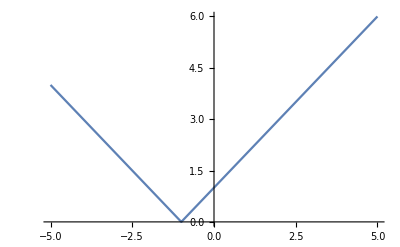

```mathematica
Plot[{Abs[x+1],neki},{x,-5,5}]
```

5 Naloga

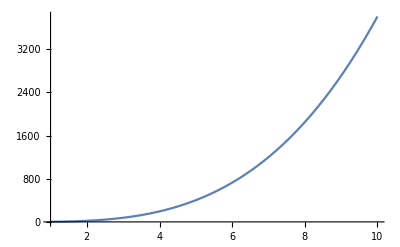

```mathematica
Naloga 5
f[x_]:=x^3 Log[4x+5]
Plot[f[x],{x,1,10}]
```

```mathematica
f[x]/.x->5
```

125 Log[25]

Solve::naqs: x0 is not a quantified system of equations and inequalities.

```mathematica
x0=5
```

5

```mathematica
f [x0]
```

125 Log[25]

```mathematica
x0=5
k0=D[f[x],x]/.x->x0
```

```mathematica
n0=n/.First[Solve[f[x0]==k0*x0+n,n]
```

```mathematica
n0=n /.First[Solve[f[x0]==k0*x0+n,n]]
```

```mathematica
t[x_]:k0*x+n0
```

```mathematica
Plot [{f[x],t[x]},{x,1,10}]
```

-Graphics-

```mathematica
Man
```